```mathematica
Manipulate[Plot[√((Cos[α] - Cos[β])^2+(Sin[α] - Sin[β])^2), {α, 0,2π}],{β,0,2π}]
```

```mathematica
Manipulate[Plot[{Abs[Sin[α]]^p,p Abs[Sin[α]]^(-1+p) Cos[α] Sign[α]},{α,-π,π}],{{p, 1}, 1, 2}]
```

Plot of regularization term and its first two derivatives for a particular p between 1 and 2. The second derivatives for the well-behaved p=1 and p=2 cases are also plotted.

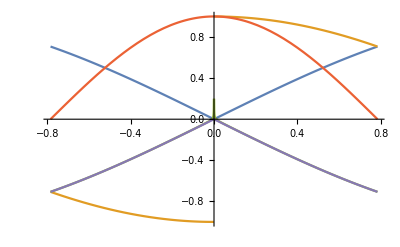

```mathematica
With[{p=1.0001},Plot[{1/p Abs[Sin[α]]^p, Abs[Sin[α]]^(-1+p) Cos[α] Sign[α], (p-1) Abs[Sin[α]]^(-2+p) Cos[α]^2-Abs[Sin[α]]^(-1+p) Sin[α] Sign[α], Cos[2 α],-Abs[Sin[α]]},{α,-π/4,π/4},ImageSize->Full]]
```

For all 1<p<2, the second derivative blows up at α=0. We investigate the behavior for α near zero over this range of p values.

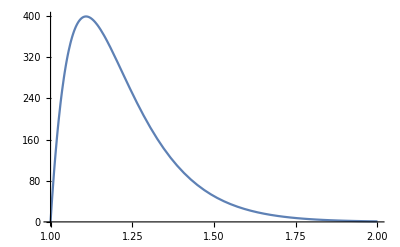

```mathematica
With[{α=10^-4},Plot[(p-1) Abs[Sin[α]]^(-2+p) Cos[α]^2-Abs[Sin[α]]^(-1+p) Sin[α] Sign[α],{p, 1, 2}]]
```